```mathematica
Clear["context`*"]
α *(Δp^2+Δv1^2+Δv2^2)+(β1+β2) (Δp^2+Δv1^2+Δv2^2)^2+(β3+β4+β5) (Δp^4+Δv1^4+Δv2^4)
(*FullSimplify[%,Assumptions->{{α,β1,β2,β3,β4,β5}∈Reals&&Δp≥0&&Δv2≥0&&Δv1≥0}]*)
a1=Expand@%
Collect[%,{Δp,Δv1,Δv2}]
α (Δp^2+Δv1^2+Δv2^2)+2 (β1+β2) (Δp^2 Δv1^2+Δp^2 Δv2^2+Δv2^2 Δv1^2)+(β1+β2+β3+β4+β5) (Δp^4+Δv1^4+Δv2^4)
Expand@%
a2=Collect[%,{Δp,Δv1,Δv2}]
FullSimplify[a1==a2,Assumptions->{{α,β1,β2,β3,β4,β5}∈Reals&&Δp≥0&&Δv2≥0&&Δv1≥0}]
```

α (Δp^2+Δv1^2+Δv2^2)+(β1+β2) (Δp^2+Δv1^2+Δv2^2)^2+(β3+β4+β5) (Δp^4+Δv1^4+Δv2^4)

α Δp^2+β1 Δp^4+β2 Δp^4+β3 Δp^4+β4 Δp^4+β5 Δp^4+α Δv1^2+2 β1 Δp^2 Δv1^2+2 β2 Δp^2 Δv1^2+β1 Δv1^4+β2 Δv1^4+β3 Δv1^4+β4 Δv1^4+β5 Δv1^4+α Δv2^2+2 β1 Δp^2 Δv2^2+2 β2 Δp^2 Δv2^2+2 β1 Δv1^2 Δv2^2+2 β2 Δv1^2 Δv2^2+β1 Δv2^4+β2 Δv2^4+β3 Δv2^4+β4 Δv2^4+β5 Δv2^4

(β1+β2+β3+β4+β5) Δp^4+(β1+β2+β3+β4+β5) Δv1^4+α Δv2^2+(β1+β2+β3+β4+β5) Δv2^4+Δv1^2 (α+(2 β1+2 β2) Δv2^2)+Δp^2 (α+(2 β1+2 β2) Δv1^2+(2 β1+2 β2) Δv2^2)

α (Δp^2+Δv1^2+Δv2^2)+2 (β1+β2) (Δp^2 Δv1^2+Δp^2 Δv2^2+Δv1^2 Δv2^2)+(β1+β2+β3+β4+β5) (Δp^4+Δv1^4+Δv2^4)

α Δp^2+β1 Δp^4+β2 Δp^4+β3 Δp^4+β4 Δp^4+β5 Δp^4+α Δv1^2+2 β1 Δp^2 Δv1^2+2 β2 Δp^2 Δv1^2+β1 Δv1^4+β2 Δv1^4+β3 Δv1^4+β4 Δv1^4+β5 Δv1^4+α Δv2^2+2 β1 Δp^2 Δv2^2+2 β2 Δp^2 Δv2^2+2 β1 Δv1^2 Δv2^2+2 β2 Δv1^2 Δv2^2+β1 Δv2^4+β2 Δv2^4+β3 Δv2^4+β4 Δv2^4+β5 Δv2^4

(β1+β2+β3+β4+β5) Δp^4+(β1+β2+β3+β4+β5) Δv1^4+α Δv2^2+(β1+β2+β3+β4+β5) Δv2^4+Δv1^2 (α+(2 β1+2 β2) Δv2^2)+Δp^2 (α+(2 β1+2 β2) Δv1^2+(2 β1+2 β2) Δv2^2)

True

```mathematica
Clear["context`*:"]
f=(α+ηp) Δp2+(α+ηv) (Δv12+Δv22)+β12 (Δp2+Δv12+Δv22)^2+β345 (Δp2^2+Δv12^2+Δv22^2)
e1=FullSimplify[D[f,Δp2],Assumptions->{{Δp2,Δv12,Δv22,β12,β345,α,ηp,ηv}∈Reals&&Δp2≥0&&Δv12≥0&&Δv22≥0&&ηp<ηv}]
e2=FullSimplify[D[f,Δv12],Assumptions->{{Δp2,Δv12,Δv22,β12,β345,α,ηp,ηv}∈Reals&&Δp2≥0&&Δv12≥0&&Δv22≥0&&ηp<ηv}]
e3=FullSimplify[D[f,Δv22],Assumptions->{{Δp2,Δv12,Δv22,β12,β345,α,ηp,ηv}∈Reals&&Δp2≥0&&Δv12≥0&&Δv22≥0&&ηp<ηv}]
Solve[{e1==0,e2==0,e3==0},{Δp2,Δv12,Δv22}]
```

β12 (Δp2+Δv12+Δv22)^2+β345 (Δp2^2+Δv12^2+Δv22^2)+Δp2 (α+ηp)+(Δv12+Δv22) (α+ηv)

α+2 β345 Δp2+2 β12 (Δp2+Δv12+Δv22)+ηp

α+2 β345 Δv12+2 β12 (Δp2+Δv12+Δv22)+ηv

α+2 β345 Δv22+2 β12 (Δp2+Δv12+Δv22)+ηv

{{Δp2→-(α β345+2 β12 ηp+β345 ηp-2 β12 ηv)/(2 β345 (3 β12+β345)),Δv12→-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345)),Δv22→-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345))}}

```mathematica
Clear["context`*"]
Clear[β0,α,t,ηp,ηv]
β1=-6/10 β0;β2=6/5 β0;β3=6/5 β0;β4=6/5 β0;β5=-6/5 β0;
β12=β1+β2;
β345=β3+β4+β5;
Δp2=-(α β345+2 β12 ηp+β345 ηp-2 β12 ηv)/(2 β345 (3 β12+β345));
Δv12=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
Δv22=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
FullSimplify[Δp2,Assumptions->{{α,β0,ηp,ηv}∈Reals&&β0>0}]
FullSimplify[Δv12,Assumptions->{{α,β0,ηp,ηv}∈Reals&&β0>0}]
FullSimplify[Δv22,Assumptions->{{α,β0,ηp,ηv}∈Reals&&β0>0}]
Reduce[{Δp2≥0,Δv12≥0,Δv22≥0,β0>0,{α,ηp,ηv,β0,N0}∈Reals,ηp<ηv,α>=-N0,N0>0},{ηp,ηv}]
Reduce[{Δp2≥0,Δv12<0,Δv22<0,β0>0,{α,ηp,ηv,β0,N0>0}∈Reals,ηp<ηv,α>=-N0,N0>0},{ηp,ηv}];
Level[%,{1}][[2]]
(*TreeForm@%*)

Reduce[{Δp2>0,Δv12≥0,Δv22≥0,β0>0,{α,ηp,ηv,β0}∈Reals,ηp<ηv},{ηp,ηv}]
```

-(α+2 ηp-ηv)/(6 β0)

(-2 α+ηp-3 ηv)/(12 β0)

(-2 α+ηp-3 ηv)/(12 β0)

(α<0&&N0≥-α&&β0>0&&ηp<-α&&ηp<ηv≤1/3 (-2 α+ηp))||(α≥0&&N0>0&&β0>0&&ηp<-α&&ηp<ηv≤1/3 (-2 α+ηp))

(α<0&&N0≥-α&&β0>0&&((ηp≤-α&&ηv>1/3 (-2 α+ηp))||(ηp>-α&&ηv≥α+2 ηp)))||(α≥0&&N0>0&&β0>0&&((ηp≤-α&&ηv>1/3 (-2 α+ηp))||(ηp>-α&&ηv≥α+2 ηp)))

α∈Reals&&β0>0&&ηp<-α&&ηp<ηv≤1/3 (-2 α+ηp)

```mathematica
Clear[t,α,ηp,ηv,N0]
α=N0 (t-1);
Reduce[ηp<-α&&{t,ηp,ηv,N0}∈Reals&&N0>0,t,Reals]
Reduce[ηp<1/3 (-2 α+ηp)&&{t,ηp,ηv,N0}∈Reals&&N0>0,t,Reals]
```

N0>0&&t<(N0-ηp)/N0

N0>0&&t<(N0-ηp)/N0

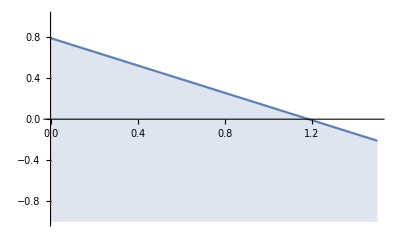
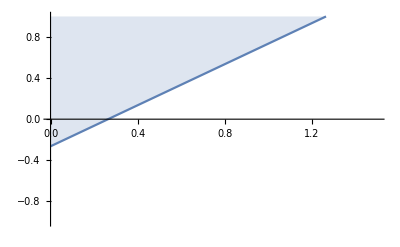

```mathematica
Clear["context`*"]
Clear[β0,α,t,ηp,ηv]
β0=1;α=t-1;ηp=0.368;
{Plot[{1/3 (-2 α+ηp)},{t,0,1.5},PlotLegends->"Expressions",Filling->Bottom,PlotRange->1],Plot[{α+2 ηp},{t,0,1.5},PlotLegends->"Expressions",Filling->Top,PlotRange->1]}
```

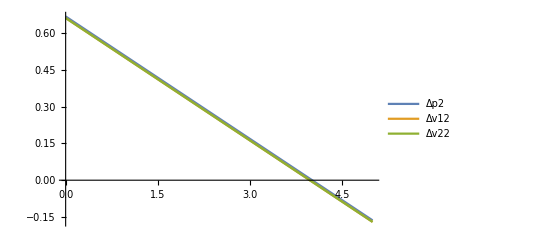

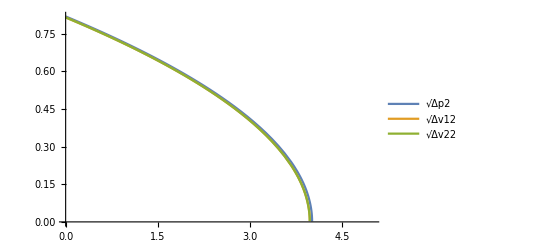

```mathematica
Clear["context`*"]
Clear[β0,α,t,ηp,ηv]
β0=1;
α=t-1;
ηp=-3;ηv=9.95/10 ηp;
β1=-6/10 β0;β2=6/5 β0;β3=6/5 β0;β4=6/5 β0;β5=-6/5 β0;
β12=β1+β2;
β345=β3+β4+β5;
Δp2=-(α β345+2 β12 ηp+β345 ηp-2 β12 ηv)/(2 β345 (3 β12+β345));
Δv12=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
Δv22=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
Plot[{Δp2,Δv12,Δv22},{t,0,5},PlotLegends->"Expressions"]
Plot[{√Δp2,√Δv12,√Δv22},{t,0,5},PlotLegends->"Expressions"]
```

0.632

0.2

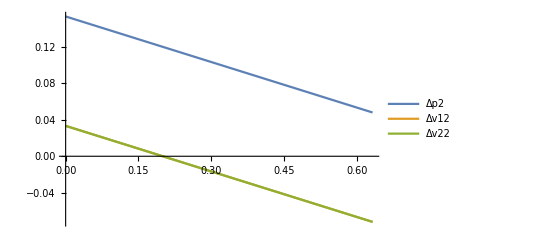

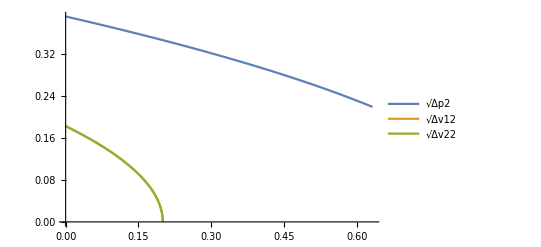

```mathematica
Clear["context`*"];Clear[β0,α,t,ηp,ηv]
β0=1;α=t-1;
ηp=0.368;ηv=0.656;(*0.2~0.72*)β1=-6/10 β0;β2=6/5 β0;β3=6/5 β0;β4=6/5 β0;β5=-6/5 β0;β12=β1+β2;β345=β3+β4+β5;
Tm2=1-ηp
Tcv=1+1/2 ηp-3/2 ηv
Δp2=-(α β345+2 β12 ηp+β345 ηp-2 β12 ηv)/(2 β345 (3 β12+β345));Δv12=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));Δv22=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
Plot[{Δp2,Δv12,Δv22},{t,0,Tm2},PlotLegends->"Expressions"]
Plot[{√Δp2,√Δv12,√Δv22},{t,0,Tm2},PlotLegends->"Expressions"]
```

0.632

0.92

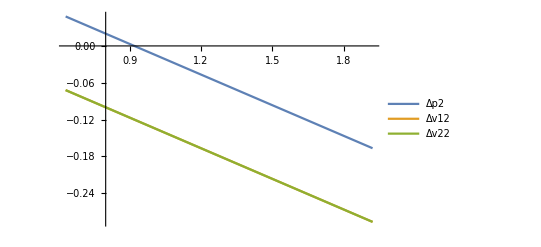

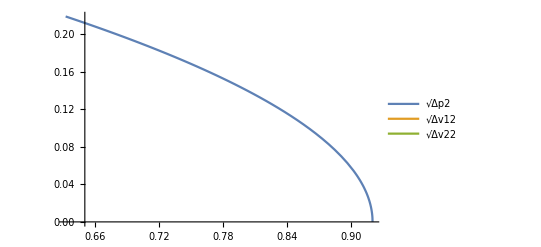

```mathematica
Clear["context`*"]
Clear[β0,α,t,ηp,ηv]
β0=1;
α=t-1;
ηp=0.368;ηv=0.656;(*ηv≥α+2ηp*)
Ts=1-ηp
Tm=1+(ηv-2 ηp)
β1=-6/10 β0;β2=6/5 β0;β3=6/5 β0;β4=6/5 β0;β5=-6/5 β0;
β12=β1+β2;
β345=β3+β4+β5;
Δp2=-(α β345+2 β12 ηp+β345 ηp-2 β12 ηv)/(2 β345 (3 β12+β345));
Δv12=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
Δv22=-(α β345-β12 ηp+β12 ηv+β345 ηv)/(2 β345 (3 β12+β345));
Plot[{Δp2,Δv12,Δv22},{t,Ts,Tm+1},PlotLegends->"Expressions"]
Plot[{√Δp2,√Δv12,√Δv22},{t,Ts,Tm+0},PlotLegends->"Expressions"]
```

```mathematica
Clear[ηvR,ηpR]
Solve[{1+ηvR-2 ηpR==0.92,1+1/2 (ηpR-3 ηvR)==0.2},{ηpR,ηvR}]
```

{{ηpR→0.368,ηvR→0.656}}

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3];
f1=(Cos[θ])^2 (Δp+Δv1)^2+Cos[θ] (Δp Δv2+Δv1 Δv2+Δp Δv2+Δv2 Δv1)+Δv2^2;
f2=(Cos[θ])^2 (Δp^2+Δv1^2)-2 Δp Δv1 (Sin[θ])^2+Δv2^2;
f3=2/3 (Δp^2+Δv1^2+Δv2^2);
fsoc=3/5 g (f1+f2-f3);
FullSimplify[Expand@fsoc,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤2 π&&Δp>Δv2&&Δp>Δv1}]
(*fsoc1=g(Δp^2+Δv1^2+2 Δv2^2+2 Δv2 (Δp+Δv1) Cos[θ]+(Δp+Δv1)^2 Cos[2 θ]);
FullSimplify[Expand@fsoc1==Expand@fsoc,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π}]*)
Print[Style["**********************************************************************",18,Red]]
FullSimplify[D[fsoc,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[D[%,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
```

1/5 g (Δp^2+Δv1^2+4 Δv2^2+6 (Δp+Δv1) Δv2 Cos[θ]+3 (Δp+Δv1)^2 Cos[2 θ])

**********************************************************************

-6/5 g (Δp+Δv1) (Δv2+2 (Δp+Δv1) Cos[θ]) Sin[θ]

-6/5 g (Δp+Δv1) (Δv2 Cos[θ]+2 (Δp+Δv1) Cos[2 θ])

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3];
f1=Cos[θ] Cos[θ] (Δp+Δv1)^2+Cos[θ] (Δp Δv2+Δv1 Δv2+Δp Δv2+Δv2 Δv1)+Δv2^2;
f2=Cos[θ] Cos[θ] (Δp^2+Δv1^2)-2 Δp Δv1 Sin[θ] Sin[θ]+Δv2^2;
f3=2/3 (Δp^2+Δv1^2+Δv2^2);
fsoc=3/5 g (f1+f2+f3);
fsocO2=3/5 g (f1+f2);
FullSimplify[fsoc,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤2 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[fsocO2,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
(*fsoc1=g(Δp^2+Δv1^2+2 Δv2^2+2 Δv2 (Δp+Δv1) Cos[θ]+(Δp+Δv1)^2 Cos[2 θ]);
FullSimplify[Expand@fsoc1==Expand@fsoc,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π}]*)
Print[Style["********** Jaakko's Formula of SOC **********",18,Red]]
FullSimplify[D[fsoc,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[D[%,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[D[fsocO2,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
```

1/5 g (5 (Δp^2+Δv1^2)+8 Δv2^2+6 (Δp+Δv1) Δv2 Cos[θ]+3 (Δp+Δv1)^2 Cos[2 θ])

3/5 g (Δp^2+Δv1^2+2 Δv2^2+2 (Δp+Δv1) Δv2 Cos[θ]+(Δp+Δv1)^2 Cos[2 θ])

********** Jaakko's Formula of SOC **********

-6/5 g (Δp+Δv1) (Δv2+2 (Δp+Δv1) Cos[θ]) Sin[θ]

-6/5 g (Δp+Δv1) (Δv2 Cos[θ]+2 (Δp+Δv1) Cos[2 θ])

-6/5 g (Δp+Δv1) (Δv2+2 (Δp+Δv1) Cos[θ]) Sin[θ]

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3,s];
f1=(Cos[θ])^2 (Δp+Δv1)^2+Cos[θ] (Δp Δv2+Δv1 Δv2+Δp Δv2+Δv2 Δv1)+Δv2^2;
f2=(Cos[θ])^2 (Δp^2+Δv1^2)-2 Δp Δv1 (Sin[θ])^2+Δv2^2;
f3=2/3 (Δp^2+Δv1^2+Δv2^2);
fsoc=3/5 g (f1+f2-f3);
Print[Style["****** θ for minium fsoc *******",18,Red]]
s=Solve[-6/5 g (Δp+Δv1) (Δv2+2 (Δp+Δv1) Cos[θ]) Sin[θ]==0&&{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1,θ,Reals]
Print[Style["***** fsoc in minium θ ******",18,Red]]
FullSimplify[fsoc/.s[[3]],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1}]
```

****** θ for minium fsoc *******

{{θ→ConditionalExpression[0,0<Δv1<Δp&&0<Δv2<Δp&&g>0&&Δp>0]},{θ→ConditionalExpression[π,0<Δv1<Δp&&0<Δv2<Δp&&g>0&&Δp>0]},{θ→ConditionalExpression[ArcCos[-Δv2/(2 (Δp+Δv1))],0<Δv1<Δp&&0<Δv2<Δp&&g>0&&Δp>0]}}

***** fsoc in minium θ ******

-2/5 g (Δp^2+3 Δp Δv1+Δv1^2)+(g Δv2^2)/2

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3,s];
f1=(Cos[θ])^2 (Δp+Δv1)^2+Cos[θ] (Δp Δv2+Δv1 Δv2+Δp Δv2+Δv2 Δv1)+Δv2^2;
f2=(Cos[θ])^2 (Δp^2+Δv1^2)-2 Δp Δv1 (Sin[θ])^2+Δv2^2;
f3=2/3 (Δp^2+Δv1^2+Δv2^2);
fsoc=3/5 g (f1+f2-f3);
FullSimplify[D[fsoc,Δp],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[D[fsoc,Δv1],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[D[fsoc,Δv2],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[fsoc/.{Δv1->0,Δv2->0},Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
```

2/5 g (Δp+3 Δv2 Cos[θ]+3 (Δp+Δv1) Cos[2 θ])

2/5 g (Δv1+3 Δv2 Cos[θ]+3 (Δp+Δv1) Cos[2 θ])

2/5 g (4 Δv2+3 (Δp+Δv1) Cos[θ])

1/5 g Δp^2 (1+3 Cos[2 θ])

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3];
f1=(Sin[θ])^2 (Δp-Δv1)^2+Sin[θ] (-Δp Δv2+Δv1 Δv2-Δp Δv2+Δv2 Δv1)+Δv2^2;
f2=(Sin[θ])^2 (Δp^2+Δv1^2)+2 Δp Δv1 (Cos[θ])^2+Δv2^2;
f3=2/3 (Δp^2+Δv1^2+Δv2^2);
fsoc=3/5 g (f1+f2-f3);
FullSimplify[Expand@fsoc,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤2 π&&Δp>Δv2&&Δp>Δv1}]
(*fsoc1=g(Δp^2+Δv1^2+2 Δv2^2+2 Δv2 (Δp+Δv1) Cos[θ]+(Δp+Δv1)^2 Cos[2 θ]);
FullSimplify[Expand@fsoc1==Expand@fsoc,Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π}]*)
Print[Style["*************** Use New θ parametrization ****************",18,Red]]
FullSimplify[D[fsoc,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
FullSimplify[D[%,θ],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤1 π&&Δp>Δv2&&Δp>Δv1}]
```

1/5 g (Δp^2+Δv1^2+4 Δv2^2-3 (Δp-Δv1)^2 Cos[2 θ]+6 (-Δp+Δv1) Δv2 Sin[θ])

*************** Use New θ parametrization ****************

6/5 g (Δp-Δv1) Cos[θ] (-Δv2+2 (Δp-Δv1) Sin[θ])

6/5 g (Δp-Δv1) (2 (Δp-Δv1) Cos[2 θ]+Δv2 Sin[θ])

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3,s];
f1=(Sin[θ])^2 (Δp+Δv1)^2+Sin[θ] (Δp Δv2+Δv1 Δv2+Δp Δv2+Δv2 Δv1)+Δv2^2;
f2=(Sin[θ])^2 (Δp^2+Δv1^2)-2 Δp Δv1 (Cos[θ])^2+Δv2^2;
f3=2/3 (Δp^2+Δv1^2+Δv2^2);
fsoc=3/5 g (f1+f2-f3);
Print[Style["****** θ for minium fsoc with new parametrization *******",18,Red]]
s=Solve[6/5 g (Δp-Δv1) Cos[θ] (-Δv2+2 (Δp-Δv1) Sin[θ])==0&&{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1,θ,Reals]
s2=Reduce[6/5 g (Δp-Δv1) Cos[θ] (-Δv2+2 (Δp-Δv1) Sin[θ])==0&&{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1&&Δv1==Δv2,θ,Reals]
Print[Style["***** fsoc in minium θ ******",18,Red]]
FullSimplify[fsoc/.s[[1]],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1}]
```

****** θ for minium fsoc with new parametrization *******

{{θ→ConditionalExpression[π/2,0<Δv1<Δp&&0<Δv2<Δp&&g>0&&Δp>0]},{θ→ConditionalExpression[π-ArcSin[Δv2/(2 (Δp-Δv1))],(0<Δv1≤Δp/2&&0<Δv2<Δp&&g>0&&Δp>0)||(0<Δv2≤2 Δp-2 Δv1&&Δp/2<Δv1<Δp&&g>0&&Δp>0)]},{θ→ConditionalExpression[ArcSin[Δv2/(2 (Δp-Δv1))],(0<Δv1≤Δp/2&&0<Δv2<Δp&&g>0&&Δp>0)||(0<Δv2≤2 Δp-2 Δv1&&Δp/2<Δv1<Δp&&g>0&&Δp>0)]}}

g>0&&Δp>0&&((0<Δv1<Δp&&Δv2==Δv1&&θ==π/2)||(0<Δv1≤(2 Δp)/3&&Δv2==Δv1&&(θ==π+ArcSin[Δv1/(2 (-Δp+Δv1))]||θ==-ArcSin[Δv1/(2 (-Δp+Δv1))])))

***** fsoc in minium θ ******

2/5 g (2 Δp^2+2 Δv1^2+3 Δv1 Δv2+2 Δv2^2+3 Δp (Δv1+Δv2))

```mathematica
Clear["context`*"];
Clear[θ,g,Δp,Δv1,Δv2,fsoc,fsoc1,f1,f2,f3,s];
FullSimplify[6/5 g (Δp-Δv1) Cos[θ] (-Δv2+2 (Δp-Δv1) Sin[θ])/.θ->π-ArcSin[Δv2/(2 (Δp-Δv1))],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1&&Δv1==Δv2}]
FullSimplify[6/5 g (Δp-Δv1) Cos[θ] (-Δv2+2 (Δp-Δv1) Sin[θ])/.θ->-ArcSin[Δv2/(2 (Δp-Δv1))],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1&&Δv1==Δv2}]
FullSimplify[-1/2 Cos[2 π-2 ArcSin[Δv2/(2 (Δp-Δv1))]],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1&&Δv1==Δv2}]
FullSimplify[-1/2 Cos[2 ArcSin[Δv2/(2 (Δp-Δv1))]],Assumptions->{{g,Δp,Δv1,Δv2,θ}∈Reals&&g>0&&Δp>0&&Δv1>0&&Δv2>0&&θ≥0&&θ≤π&&Δp>Δv2&&Δp>Δv1&&Δv1==Δv2}]
%/.Δv2->0
π-ArcSin@0
ArcSin@0
```

0

-6/5 g Δv2 √(4 Δp^2-8 Δp Δv2+3 Δv2^2)

1/2 Cos[2 ArcCos[Δv2/(2 Δp-2 Δv2)]]

1/2 Cos[2 ArcCos[Δv2/(2 Δp-2 Δv2)]]

-1/2

π

0

```mathematica
Integrate[1/Sin[θ],θ]
```

-Log[Cos[θ/2]]+Log[Sin[θ/2]]